```mathematica
dat=ReadList["global-data.dat"];
datSolitons=ReadList["solitons.txt"][[1]];
```

```mathematica
w=dat[[All,1]];
alpha=dat[[All,2]];
nr=dat[[All,3]];
Mint=-dat[[All,4]];
Jint=dat[[All,5]];
Q=dat[[All,6]];
MH =dat[[All,-9]];
JH =dat[[All,-8]];
Mass =dat[[All,-7]];
MInt=-dat[[All,-6]];
TH=dat[[All,-2]];
rh=dat[[All,-1]];
```

```mathematica
wSolitons = datSolitons[[All,1]];
MSolitons = datSolitons[[All,4]];
JSolitons = datSolitons[[All,5]];
```

```mathematica
len=Length[dat];
lenSolitons=Length[datSolitons];
solitonwM=ListPlot[Table[{wSolitons[[i]],MSolitons[[i]]},{i,1,lenSolitons}],PlotStyle->  Red];
```

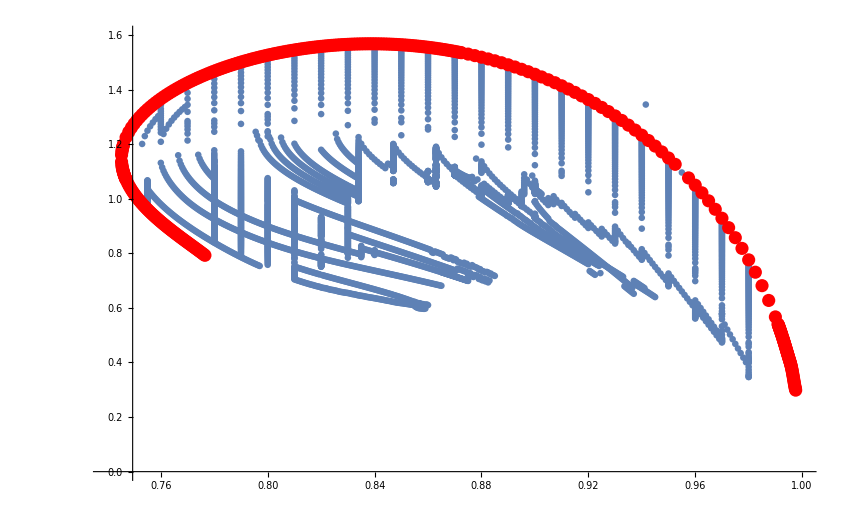

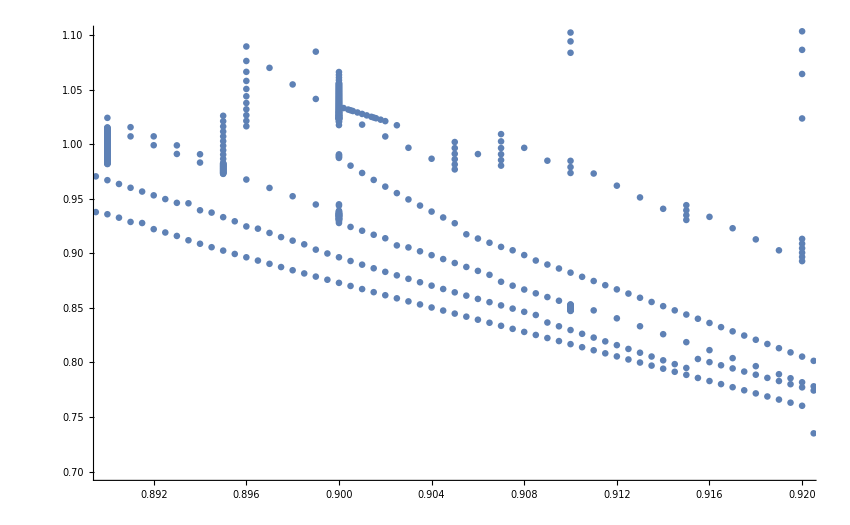

```mathematica
m=ListPlot[Table[{w[[i]],Mass[[i]]},{i,1,len}]];
Show[m,solitonwM,PlotRange->{{0.74,1},{0.,1.6}}]
Show[m,solitonwM,PlotRange->{{0.89,0.92},{0.7,1.1}}]
```

```mathematica
ListPlot[Table[{rh[[i]],Mint[[i]]},{i,1,len}],PlotRange->{{0.,0.3},{0.0,1.6}}]
```

-Graphics-

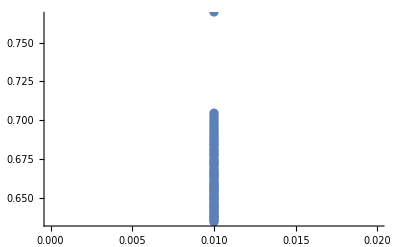

```mathematica
ListPlot[Table[{rh[[i]],Mass[[i]]},{i,1,len}]]
```

```mathematica
p1=ListPlot[Table[{w[[i]],MH[[i]]},{i,1,len}]];
p2=ListPlot[Table[{w[[i]],Mint[[i]]},{i,1,len}],PlotStyle->Green];
p3=ListPlot[Table[{w[[i]],Mass[[i]]},{i,1,len}],PlotStyle->Red];
Show[p1,p2,p3,PlotRange->{{0.73,1},{0,1.6}}]
```

-Graphics-

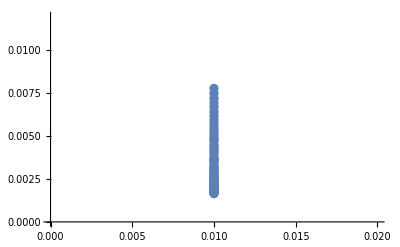

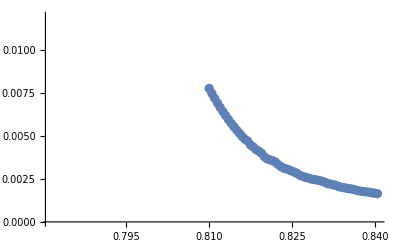

```mathematica
ListPlot[Table[{rh[[i]],TH[[i]]Mass[[i]]},{i,1,len}]]
ListPlot[Table[{w[[i]],TH[[i]]Mass[[i]]},{i,1,len}]]
```